```mathematica
BoxGfx[point_]:=Graphics[Line[{point,point+{0,1},point+{1,1},point+{1,0},point}]];
BoxNetwork[n_]:=Module[{i,points,cp,adj,gfxlist},
points={{0,0}};
cp={0,0};
For[i=1,i≤n,i++,
adj=RandomInteger[{-Floor[Sqrt[n]],Floor[Sqrt[n]]}];
If[Mod[i,2]==0,
cp=cp+{0,adj};
,
cp=cp+{adj,0};
];
AppendTo[points,cp];
];
gfxlist={BoxGfx[{0,0}]};
For[i=2,i≤Length[points],i++,
AppendTo[gfxlist,BoxGfx[points[[i]]]];
];
Show[gfxlist]
];
```

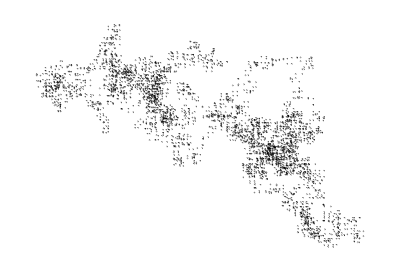

```mathematica
BoxNetwork[4000]
```